## Inicializaciones

```mathematica
sizeP=201;
```

```mathematica
sizeC=2;
```

```mathematica
θA=π/2.;
```

```mathematica
θBplus=π/4.;
```

```mathematica
θBminus= -π/8.;
```

## Definiciones

### Funciones externas

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Espacios de Hilbert

```mathematica
baseP=IdentityMatrix[sizeP];
```

```mathematica
baseC=IdentityMatrix[sizeC];
```

### Funciones bra y ket

```mathematica
bra[c_,p_]:=KroneckerProduct[{baseC[[c+1]]},{baseP[[p+1+(sizeP-1)/2]]}]
```

```mathematica
ket[c_,p_]:=ConjugateTranspose[bra[c,p]]
```

```mathematica
braP[p_]:={baseP[[p+1+(sizeP-1)/2]]}
```

```mathematica
braC[c_]:={baseC[[c+1]]}
```

```mathematica
ketP[p_]:=braP[p]†
```

```mathematica
ketC[c_]:=braC[c]†
```

### Operadores

```mathematica
MatrixExp[-ⅈ  θ  PauliMatrix[2]/2]
```

{{Cos[θ/2],-Sin[θ/2]},{Sin[θ/2],Cos[θ/2]}}

```mathematica
coinA=KroneckerProduct[{{Cos[θA/2],-Sin[θA/2]},{Sin[θA/2],Cos[θA/2]}},baseP];
```

```mathematica
θB[x_]:=(θBplus(1+Tanh[x])+θBminus(1-Tanh[x]))/2
```

```mathematica
coinB=Sum[
KroneckerProduct[{{Cos[θB[x]/2],-Sin[θB[x]/2]},{Sin[θB[x]/2],Cos[θB[x]/2]}},ketP[x].braP[x]],
{x,-(sizeP-1)/2, (sizeP-1)/2}
];
```

```mathematica
(* S = \sum_i |0, i+1\rangle\langle 0, i|  + \sum_i |1, i-1\rangle\langle 1, i| *)
```

```mathematica
shift=Sum[ket[0,i+1].bra[0,i],{i,-(sizeP-1)/2,(sizeP-1)/2-1}]+Sum[ket[1,i-1].bra[1,i],{i,-(sizeP-1)/2+1,(sizeP-1)/2}];
```

```mathematica
Unitary[m_Integer,n_Integer]:=shift.Dot@@Join[Table[coinA,m],Table[coinB,n]]
```

### Distribución de probabilidad respecto al tiempo y el valor de expectación respecto al tiempo

```mathematica
ProbDisTime[initialState_,m_Integer,n_Integer]:=
Module[{state=initialState,probs},
Table[
probs=Abs@Diagonal@MatrixPartialTrace[state.state†,1,{sizeC,sizeP}];
state=Unitary[m,n].N[state];
probs,
(sizeP-1)/2+1
]
]
```

```mathematica
ExpecValue[probDisTime_List]:=Flatten[probDisTime.Table[{i},{i,-(sizeP-1)/2,(sizeP-1)/2}]]
```

### Funciones para graficar

#### Probabilidad respecto al tiempo

```mathematica
PlotProbDisTime[probDisTime_List]:=
ArrayPlot[probDisTime,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
PlotLegends->Automatic,
ColorFunction->"BlueGreenYellow",
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(sizeP-1)/2+1,20}],None},{Table[{i,i-1-(sizeP-1)/2,0},{i,1,sizeP,100}],None}},
FrameTicksStyle->13,
PlotRangePadding->0
]
```

#### Valor de expectación respecto al tiempo

```mathematica
PlotExpecValue[expecValue_List,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,(sizeP-1)/2],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->50,
PlotStyle->Thickness[0.005],
Evaluate@opts
]
```

```mathematica
PlotExpecValue[{expecValues__List},opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,(sizeP-1)/2],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->50,
Evaluate@opts
]
```

```mathematica
DownValues[PlotExpecValue]
```

{HoldPattern[PlotExpecValue[{expecValues__List},opts:OptionsPattern[ListLinePlot]]]:>ListLinePlot[(Transpose[{Range[0,(sizeP-1)/2],#1}]&)/@{expecValues},BaseStyle→{FontFamily→Latin Modern Roman},PlotRange→All,Frame→True,AspectRatio→1,FrameLabel→(#1&)/@{,},FrameTicksStyle→13,Evaluate[opts]],HoldPattern[PlotExpecValue[expecValue_List,opts:OptionsPattern[ListLinePlot]]]:>ListLinePlot[Transpose[{Range[0,(sizeP-1)/2],expecValue}],BaseStyle→{FontFamily→Latin Modern Roman},PlotRange→All,Frame→True,AspectRatio→1,FrameLabel→(#1&)/@{,},FrameTicksStyle→13,Evaluate[opts]]}

## Pruebas

```mathematica
state0=ket[1,0];
```

### Losing strategies

#### Estrategia 1

```mathematica
probDistTimeL1=ProbDisTime[state0,1,0];
```

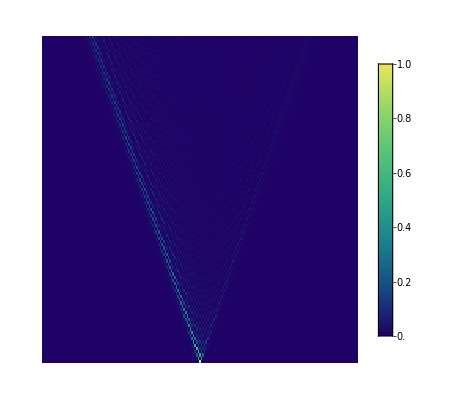

```mathematica
PlotProbDisTime@probDistTimeL1
```

```mathematica
expvalL1=ExpecValue[probDistTimeL1];
```

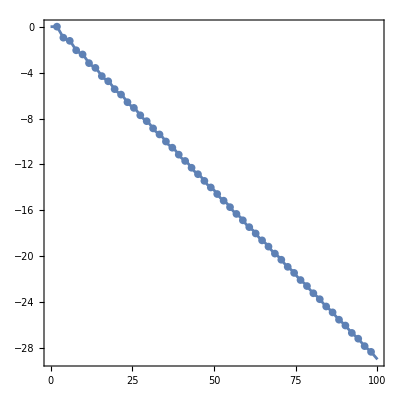

```mathematica
plotL1=PlotExpecValue[expvalL1]
```

#### Estrategia 2

```mathematica
probDistTimeL2=ProbDisTime[state0,0,1];
```

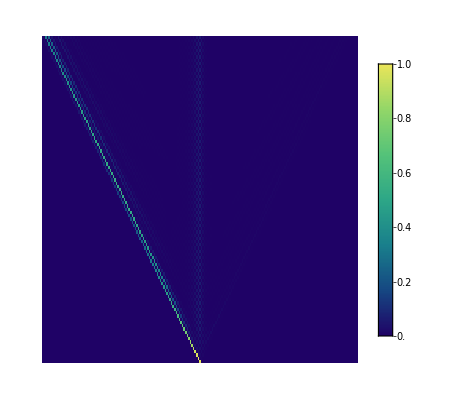

```mathematica
PlotProbDisTime@probDistTimeL2
```

```mathematica
expvalL2=ExpecValue[probDistTimeL2];
```

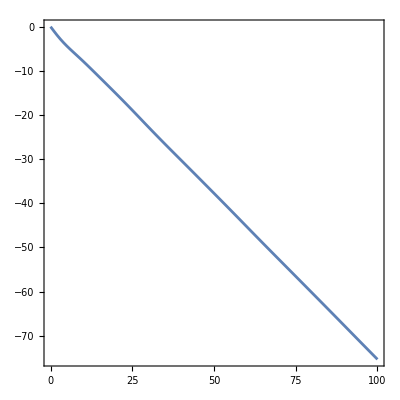

```mathematica
plotL2=PlotExpecValue[expvalL2]
```

#### Estrategia 3

```mathematica
probDistTimeL3=ProbDisTime[state0,1,1];
```

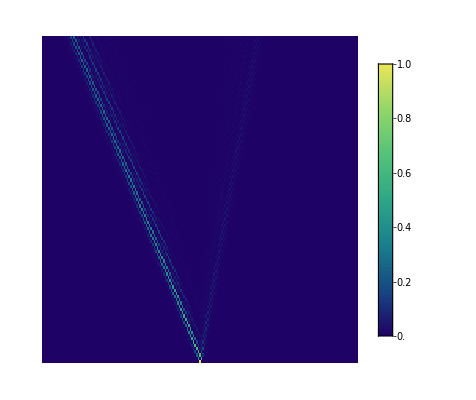

```mathematica
PlotProbDisTime@probDistTimeL3
```

```mathematica
expvalL3=ExpecValue[probDistTimeL3];
```

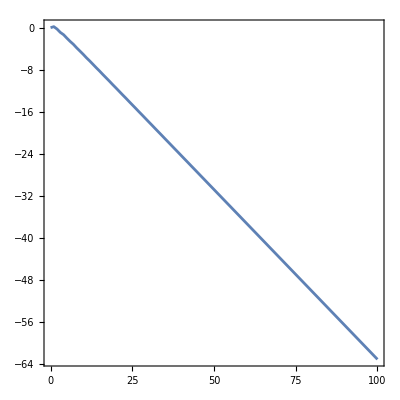

```mathematica
plotL3=PlotExpecValue[expvalL3]
```

#### Estrategia 4

```mathematica
probDistTimeL4=ProbDisTime[state0,1,2];
```

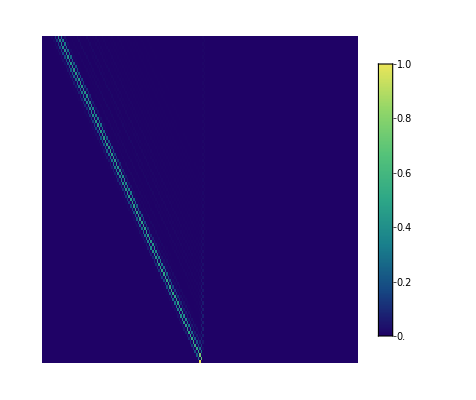

```mathematica
PlotProbDisTime@probDistTimeL4
```

```mathematica
expvalL4=ExpecValue[probDistTimeL4];
```

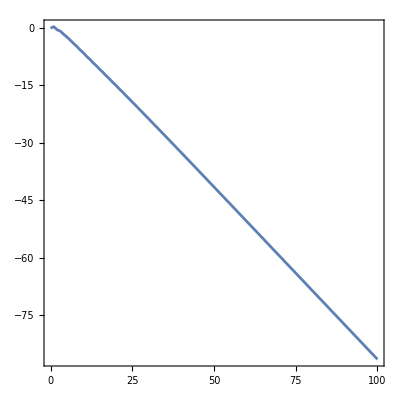

```mathematica
plotL4=PlotExpecValue[expvalL4]
```

#### Todas las estrategias perdedoras del artículo

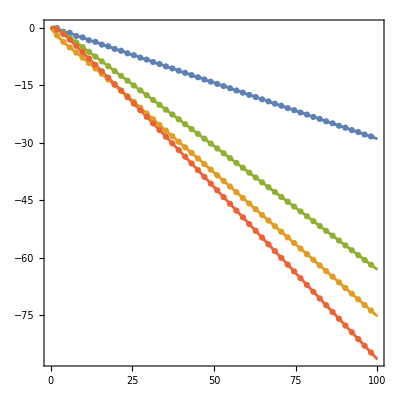

```mathematica
PlotExpecValue[{expvalL1,expvalL2,expvalL3,expvalL4},PlotLegends->{"","","",""}]
```

### Winning strategies

#### Estrategia 1

```mathematica
probDistTimeW1=ProbDisTime[state0,2,1];
```

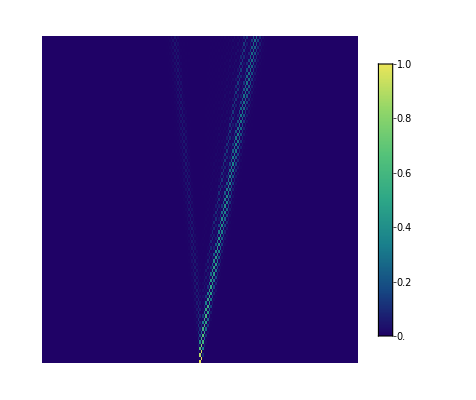

```mathematica
PlotProbDisTime@probDistTimeW1
```

```mathematica
expvalW1=ExpecValue[probDistTimeW1];
```

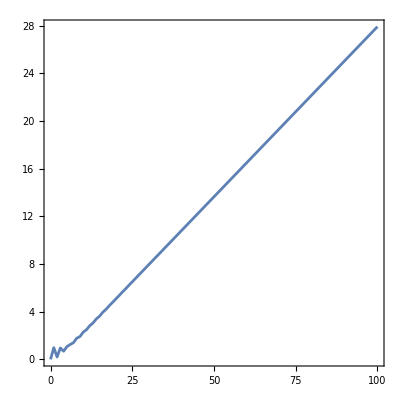

```mathematica
PlotW1=PlotExpecValue[expvalW1]
```

#### Estrategia 2

```mathematica
probDistTimeW2=ProbDisTime[state0,2,2];
```

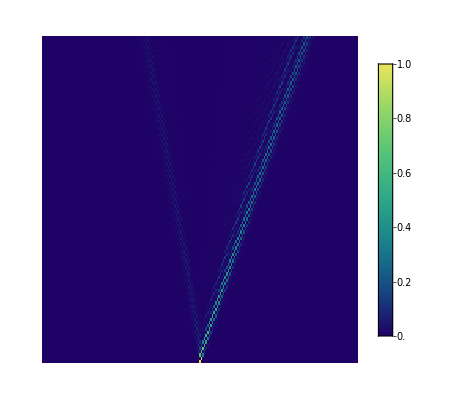

```mathematica
PlotProbDisTime@probDistTimeW2
```

```mathematica
expvalW2=ExpecValue[probDistTimeW2];
```

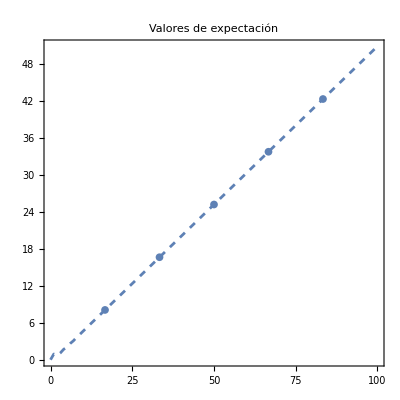

```mathematica
PlotW2=PlotExpecValue[expvalW2,PlotLabel->"Valores de expectación",PlotStyle->Dashed,Mesh->5]
```

#### Todas las estrategias ganadoras del artículo

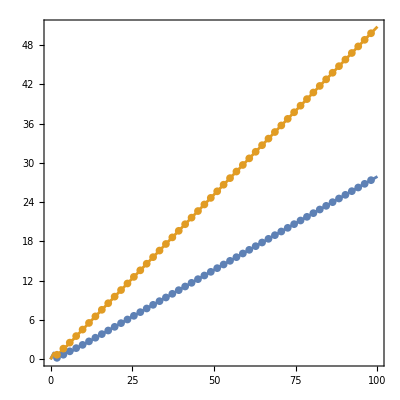

```mathematica
PlotExpecValue[{expvalW1,expvalW2},PlotLegends->{"",""}]
```